# Chapter 5: Proposal for a photon-photon gate and error analysis

## Author: Bruno Ortega Goes

## 0.Preamble

```mathematica
Nbdirectory = SetDirectory[NotebookDirectory[]];
(*Setting where to save the plots*)
PlotsPath = "/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap5/";
overleafPath="/Users/brunogoes/Dropbox/Aplicativos/Overleaf/00Bruno-Goes-ThesisDraft/Figures/Chap5/";

(*To easily insert a label*)
alphabetlabel={"(a)","(b)","(c)","(d)","(e)","(f)","(g)","(h)","(i)","(j)","(k)","(l)","(m)","(n)","(o)","(p)","(q)","(r)","(s)","(t)","(u)","(v)","(w)","(x)","(y)","(z)"};

AlphabetLabelling[x_,xpos_:0.1,ypos_:0.9] := Text["("<>ToString@x<>")",Scaled[{xpos,ypos}]];
```

## 1.Functions and Hilbert space definition

Defining the generic computational basis {|0⟩,|1⟩}

```mathematica
ket0 = {1,0};
ket1 = {0,1};
```

Defining the photonic and spin basis: {|vac,vac⟩,|vac,R⟩,,|R,vac⟩,|RR⟩}, {|↑⟩,|↓⟩}

```mathematica
Vac = ket0;
Rph = ket1;

SpUp = ket0;
SpDw = ket1;

VacVac = kron[Vac,Vac]//mf;
VacR = kron[Vac,Rph]//mf;
RVac = kron[Rph,Vac]//mf;
RR = kron[Rph,Rph]//mf;
```

(1
0
0
0)

(0
1
0
0)

(0
0
1
0)

(0
0
0
1)

```mathematica
Clear[Gup,Gdw]
Gup[r_]:=- ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -((r^2+2r-1)/2)}});
Gdw [r_]:= ({{1, 0, 0, 0}, {0, -r, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, (r^2+1)/2}}) ;
GupIdeal = Gup[1];
GdwIdeal = Gdw[1];
```

In the ideal case we have the following gates:

```mathematica
GupIdeal//mf;
GdwIdeal//mf;
```

(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## 2.Case of study: Decreasing pulse

Through this section I apply the formalism assuming a decreasing exponential pulse.

## Input and output pulse shapes

```mathematica
Intensity[funcoft_]:=funcoft funcoft*//cf
```

```mathematica
Clear[ξdec,γ,Γ,ω0];
ξdec[t_] := √(Γ/2)Exp[-(Γ/4+ⅈ ω0)t];
InputIntensityDec=Intensity[ξdec[t]];

Assuming[Γ>0,Integrate[ξdec[t] ξdec[t]*//cf, {t,0,∞}]]
```

1

```mathematica
Clear[ξdectilde];
ξdectilde[t_] :=ⅇ^(-(γ t)/2)Integrate[ⅇ^((γ/2+ⅈ ω0)s)ξdec[s],{s,0,t}] ;
ξdectilde[t]
```

-(2 √2 ⅇ^(-(t γ)/2) (-1+ⅇ^(1/4 t (2 γ-Γ))) √Γ)/(-2 γ+Γ)

```mathematica
(*Computing the output shape*)
Υdec[t_]:=γ ξdectilde[t] ⅇ^(-ⅈ ω0 t)-ξdec[t]
OutputIntensityDec=Intensity[Υdec[t]];
Assuming[{Γ>0 && γ>0},Integrate[Υdec[t] Υdec[t]*//cf, {t,0,∞}]]
```

1

```mathematica
Υdec[t]//cf
```

(ⅇ^(-1/2 t (γ+2 ⅈ ω0)) √Γ (4 γ-ⅇ^(1/4 t (2 γ-Γ)) (2 γ+Γ)))/(√2 (-2 γ+Γ))

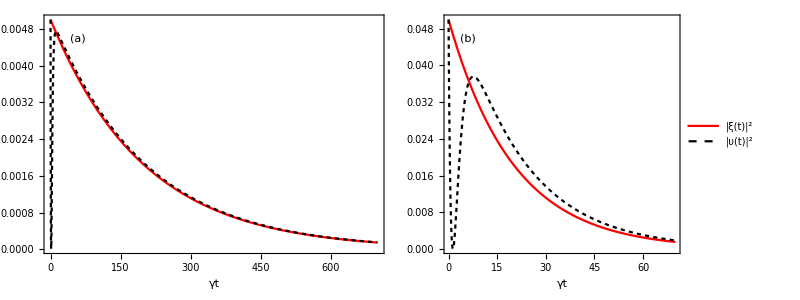

```mathematica
γ=1;

IntensityCurvesLines={{Red,Automatic},{Black,Dashing[{.01}]}};

Grid[
{
{fig1a=Plot[
{InputIntensityDec/.Γ->10^-2, OutputIntensityDec/.Γ->10^-2},{t,0,7 Γ^-1}/.Γ->10^-2,
Frame->True,
PlotStyle->IntensityCurvesLines,
PlotRange->All,
FrameStyle->Black,
ImageSize->300,
FrameLabel->{"γt",None},
Epilog->AlphabetLabelling["a"]],

fig1b=Plot[{InputIntensityDec/.Γ->10^-1, OutputIntensityDec/.Γ->10^-1},{t,0,7 Γ^-1}/.Γ->10^-1,
Frame->True,
PlotStyle->IntensityCurvesLines,
PlotRange->All,
FrameStyle->Black,
ImageSize->300,
FrameLabel->{"γt",None},
PlotLegends->legend[{"|ξ(t)|^2","|υ(t)|^2"},{0.8,0.75}],
Epilog->AlphabetLabelling["b"]]}

(*Plot[

{InputIntensityDec/.Γ->1, OutputIntensityDec/.Γ->1},{t,0,7 Γ^-1}/.Γ->1,
Frame->True,
PlotStyle->IntensityCurvesLines,
PlotRange->All,
FrameStyle->Black,
ImageSize->300,
FrameLabel->{"γt",None},
PlotLegends->legend[{"|ξ(t)|^2","|υ(t)|^2"},{0.8,0.75}],
Epilog->AlphabetLabelling["c"]]}
*)
}]
Export[overleafPath<>"Chap5DecreasingPulseShapeDiffeGammas.pdf",%];
```

## Non-monochromaticity parameter

```mathematica
m[InputOfT_,OutputOfT_]:=Module[{dummy},
dummy = InputOfT* OutputOfT//cf;
Integrate[dummy,{t,0,∞}]//cf]
```

```mathematica
Clear[γ]
mdec = m[ξdec[t],Υdec[t]]
```

-1+(4 γ)/(2 γ+Γ)

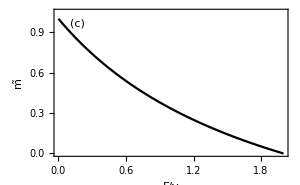

```mathematica
fig1c = Plot[mdec/.γ->1,{Γ,0,2},
Frame->True,
PlotStyle->{Black},
PlotRange->{All,{0,1.05}},
FrameStyle->Black,
ImageSize->300,
FrameLabel->{"Γ/γ","m̃"},
Epilog->AlphabetLabelling["c"]
]
Export[overleafPath<>"Chap5DecreasingNonMonochromaticity.pdf",%];
```

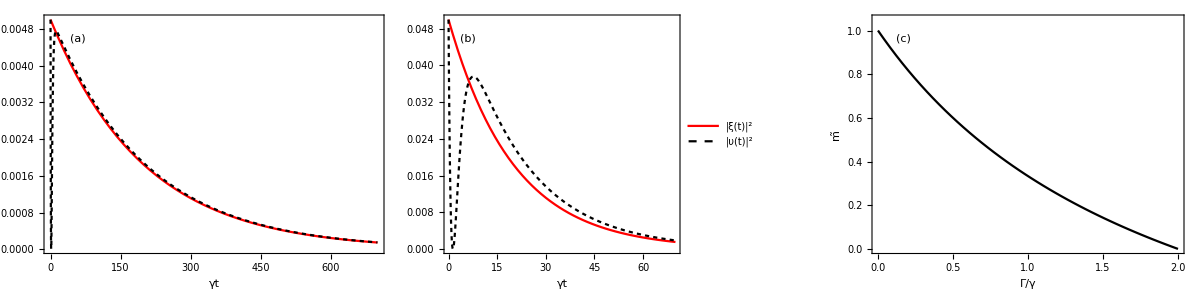

```mathematica
Grid[{{fig1a,fig1b,fig1c}}]
Export[overleafPath<>"Chap5Fig1.pdf",%];
```

## 3.Error characterization

## 3.1 Gate fidelity

We define the field initial states as in the text:

```mathematica
Φi1 =Cos[θ/2]Vac+ⅇ^(ⅈ ϕ1)Sin[θ/2]Rph //cf//mf;
Φi2 =Cos[ζ/2]Vac+ⅇ^(ⅈ ϕ2)Sin[ζ/2]Rph //cf//mf;
Φ0 = kron[Φi2,Φi1]//cf//mf;
```

(Cos[θ/2]
ⅇ^(ⅈ ϕ1) Sin[θ/2])

(Cos[ζ/2]
ⅇ^(ⅈ ϕ2) Sin[ζ/2])

(Cos[ζ/2] Cos[θ/2]
ⅇ^(ⅈ ϕ1) Cos[ζ/2] Sin[θ/2]
ⅇ^(ⅈ ϕ2) Cos[θ/2] Sin[ζ/2]
ⅇ^(ⅈ (ϕ1+ϕ2)) Sin[ζ/2] Sin[θ/2])

Quick sanity check:

```mathematica
GupIdeal==GupIdeal†
GdwIdeal==GdwIdeal†
```

True

True

Computing the ideal bra and the real final ket states for spins up and down:

```mathematica
(*The ideal final state is given by:*)
IdealFinalStateUpBra = Φ0*.GupIdeal//cf//mf;

(*The real final state is given by:*)
RealFinalStateUpKet = Gup[r].Φ0//cf//mf;
```

(-Cos[ζ/2] Cos[θ/2]
-ⅇ^(-ⅈ ϕ1) Cos[ζ/2] Sin[θ/2]
-ⅇ^(-ⅈ ϕ2) Cos[θ/2] Sin[ζ/2]
ⅇ^(-ⅈ (ϕ1+ϕ2)) Sin[ζ/2] Sin[θ/2])

(-Cos[ζ/2] Cos[θ/2]
-ⅇ^(ⅈ ϕ1) Cos[ζ/2] Sin[θ/2]
-ⅇ^(ⅈ ϕ2) Cos[θ/2] Sin[ζ/2]
1/2 ⅇ^(ⅈ (ϕ1+ϕ2)) (-1+r (2+r)) Sin[ζ/2] Sin[θ/2])

```mathematica
(*The ideal final state is given by:*)
IdealFinalStateDwBra = Φ0*.GdwIdeal//cf//mf;

(*The real final state is given by:*)
RealFinalStateDwKet = Gdw[r].Φ0//cf//mf;
```

(Cos[ζ/2] Cos[θ/2]
-ⅇ^(-ⅈ ϕ1) Cos[ζ/2] Sin[θ/2]
ⅇ^(-ⅈ ϕ2) Cos[θ/2] Sin[ζ/2]
ⅇ^(-ⅈ (ϕ1+ϕ2)) Sin[ζ/2] Sin[θ/2])

(Cos[ζ/2] Cos[θ/2]
-ⅇ^(ⅈ ϕ1) r Cos[ζ/2] Sin[θ/2]
ⅇ^(ⅈ ϕ2) Cos[θ/2] Sin[ζ/2]
1/2 ⅇ^(ⅈ (ϕ1+ϕ2)) (1+r^2) Sin[ζ/2] Sin[θ/2])

Computing the overlap between the ideal and real final states:

```mathematica
OverlapUp = IdealFinalStateUpBra.RealFinalStateUpKet//cf

OverlapDw = IdealFinalStateDwBra.RealFinalStateDwKet//cf
```

Cos[ζ/2]^2+1/4 ((1+r)^2-(-1+r) (3+r) Cos[θ]) Sin[ζ/2]^2

1/4 (2 Cos[ζ/2]^2 (1+r+Cos[θ]-r Cos[θ])+(3+r^2+Cos[θ]-r^2 Cos[θ]) Sin[ζ/2]^2)

Computing the overlap squared that goes in the fidelity:

```mathematica
ℱgateUp=OverlapUp OverlapUp*//cf
```

1/16 (2+2 Cos[ζ]+((1+r)^2-(-1+r) (3+r) Cos[θ]) Sin[ζ/2]^2)^2

```mathematica
ℱgateDw=OverlapDw OverlapDw*//cf
```

1/64 (5+r (2+r)-(-1+r) (3+r) Cos[θ]-2 (-1+r)^2 Cos[ζ] Sin[θ/2]^2)^2

It does not depend on the phase, only on the angles θ and ξ and the non-monochromaticity parameter .
Next we can numerically minimize over (θ,ξ) as a function of r and Γ.

```mathematica
MinimizedFidelityUp = Table[{r,Chop@NMinimize[ℱgateUp ,{ζ,θ}]⟦1⟧},{r,0,1,10^-2}];
MinimizedFidelityDw = Table[{r,Chop@NMinimize[ℱgateDw ,{ζ,θ}]⟦1⟧},{r,0,1,10^-2}];


MinimizedFidelityUpΓ = Table[{Γ,Chop@NMinimize[ℱgateUp/.r->mdec/.γ->1 ,{ζ,θ}]⟦1⟧},{Γ,0,1,10^-2}];
MinimizedFidelityDwΓ = Table[{Γ,Chop@NMinimize[ℱgateDw/.r->mdec/.γ->1  ,{ζ,θ}]⟦1⟧},{Γ,0,1,10^-2}];
```

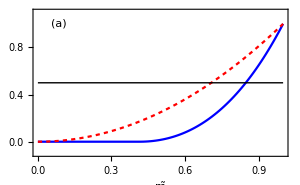
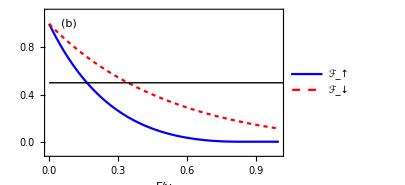

```mathematica
FidelityCurvesLines={{Blue,Automatic},{Red,Dashing[{.01}]}};

Row[{ListLinePlot[{MinimizedFidelityUp,MinimizedFidelityDw},Frame->True,PlotStyle->FidelityCurvesLines,PlotRange->{All,{-0.1,1.1}},FrameStyle->Black,ImageSize->300,FrameLabel->{"\!\(\*OverscriptBox[\(m\), \(~\)]\)",None},Epilog->{AlphabetLabelling["a"],Black,Line[{{0,0.5},{1,0.5}}]  (*Add the vertical black line*)}],ListLinePlot[{MinimizedFidelityUpΓ,MinimizedFidelityDwΓ},Frame->True,PlotStyle->FidelityCurvesLines,PlotRange->{All,{-0.1,1.1}},FrameStyle->Black,ImageSize->300,FrameLabel->{"Γ/γ",None},PlotLegends->legend[{"\!\(\*SubscriptBox[\(ℱ\), \(↑\)]\)","\!\(\*SubscriptBox[\(ℱ\), \(↓\)]\)"},{0.8,0.75}],Epilog->{AlphabetLabelling["b"],Black,Line[{{0,0.5},{2,0.5}}]  (*Add the vertical black line*)}]}]
Export[overleafPath<>"Chap5FidelitiesUpandDw.pdf",%];
```

The fidelities are different betcause the interaction between the R-photon and the spin isn’t symmetrical. From the map we now that after interacting with a spin up, the decay might not be monochromatic, hence the “non-monochromaticity” parameter will affect more the up state.

## 3.2 Error Matrix

We define the ordered Pauli basis:

```mathematica
ℬ = Table[kron[i,j],{i,{σ0,σx,σy,σz}},{j,{σ0,σx,σy,σz}}]//mf;
```

((1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)
(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)
(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1))

The error process is: χ_j^error=  ((G_j^[1]))^-1  ((G_j^[1]))^real

```mathematica
GupReal = Gup[r]//cf//mf;
GdwReal = Gdw[r]//cf//mf;
```

(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1/2 (-1+r (2+r)))

(1 | 0 | 0 | 0
0 | -r | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1/2 (1+r^2))

```mathematica
GupIdeal//mf;
GdwIdeal//mf;
```

(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Computing the error process matrix:

```mathematica
χerrorUp = ((Inverse[GupIdeal].GupReal)/4)//cf//mf;

χerrorDw = ((Inverse[GdwIdeal].GdwReal)/4)//cf//mf;
```

(1/4 | 0 | 0 | 0
0 | 1/4 | 0 | 0
0 | 0 | 1/4 | 0
0 | 0 | 0 | 1/8 (-1+r (2+r)))

(1/4 | 0 | 0 | 0
0 | r/4 | 0 | 0
0 | 0 | 1/4 | 0
0 | 0 | 0 | 1/8 (1+r^2))

Computing the trace of both error matrices:

```mathematica
traceχerrorUp=Tr[χerrorUp]//cf
traceχerrorDw=Tr[χerrorDw]//cf
```

1/8 (5+r (2+r))

1/8 (5+r (2+r))

```mathematica
traceχerrorDw/.r->1//cf
traceχerrorUp/.r->1//cf
```

1

1

## 3.3 Decomposing the real and ideal processes in the Pauli basis

Decomposition in the Pauli basis of up:

```mathematica
IdealUpDecomposition = Table[Tr[ℬ⟦i,j⟧.GupIdeal]/4,{i,1,4},{j,1,4}]//mf;

RealUpDecomposition = Table[Tr[ℬ⟦i,j⟧.GupReal]/4,{i,1,4},{j,1,4}]//cf//mf;

χerrorUpDecomposition = Table[Tr[ℬ⟦i,j⟧.χerrorUp],{i,1,4},{j,1,4}]//cf//mf;
```

(-1/2 | 0 | 0 | -1/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/2 | 0 | 0 | 1/2)

(1/8 (-7+r (2+r)) | 0 | 0 | -1/8 (1+r)^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/8 (1+r)^2 | 0 | 0 | 1/8 (1+r)^2)

(1/8 (5+r (2+r)) | 0 | 0 | -1/8 (-1+r) (3+r)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/8 (-1+r) (3+r) | 0 | 0 | 1/8 (-1+r) (3+r))

Decomposition in the Pauli basis of down:

```mathematica
IdealDwDecomposition = Table[Tr[ℬ⟦i,j⟧.GdwIdeal]/4,{i,1,4},{j,1,4}]//mf;

RealDwDecomposition = Table[Tr[ℬ⟦i,j⟧.GdwReal]/4,{i,1,4},{j,1,4}]//cf//mf;

χerrorDwDecomposition = Table[Tr[ℬ⟦i,j⟧.χerrorDw],{i,1,4},{j,1,4}]//cf//mf;
```

(1/2 | 0 | 0 | 1/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/2 | 0 | 0 | 1/2)

(1/8 (5+(-2+r) r) | 0 | 0 | -1/8 (-3+r) (1+r)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/8 (1+r)^2 | 0 | 0 | 1/8 (1+r)^2)

(1/8 (5+r (2+r)) | 0 | 0 | -1/8 (-1+r) (3+r)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/8 (-1+r)^2 | 0 | 0 | 1/8 (-1+r)^2)

The worst case possible happens for a completely non-monochromatic scattering:

```mathematica
χerrorUpDecomposition/.r->0//N//mf;

χerrorDwDecomposition/.r->0//N//mf;
```

(0.625 | 0 | 0 | 0.375
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0.375 | 0 | 0 | -0.375)

(0.625 | 0 | 0 | 0.375
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-0.125 | 0 | 0 | 0.125)

Sanity check: In the ideal scenario where the pulse is monochromatic, r=1, do we have only the upper left element =1?

```mathematica
χerrorUpDecomposition/.r->1//N//mf;

χerrorDwDecomposition/.r->1//N//mf;
```

(1. | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(1. | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Yes!

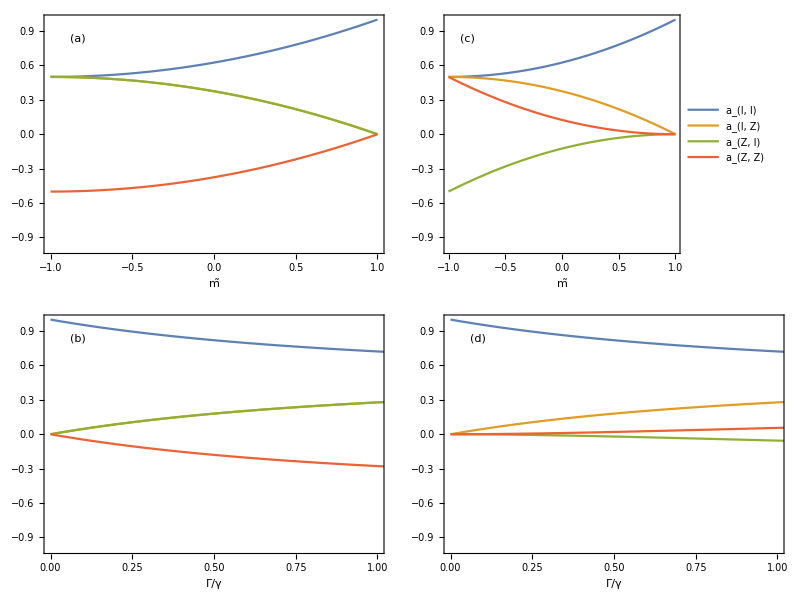

```mathematica
plotrangeamplitudes = {{-1,1},{-1,1}};
plotrangeamplitudesΓ = {{0,1},{-1,1}};

Grid[{{
(*Plotting as a function of m*)
Plot[DeleteCases[χerrorUpDecomposition//Flatten,0]//Evaluate,{r,-1,1},
Frame->True,
BaseStyle->14,
PlotRange->plotrangeamplitudes,
FrameStyle->Black,
ImageSize->325,
AxesOrigin->{-1,-1},
FrameLabel->{"m̃",None},
Epilog->AlphabetLabelling["a"]],

Plot[DeleteCases[χerrorDwDecomposition//Flatten,0]//Evaluate,{r,-1,1},Frame->True,BaseStyle->14,
PlotRange->plotrangeamplitudes,
FrameStyle->Black,
ImageSize->325,
AxesOrigin->{-1,-1},
FrameLabel->{"m̃",None},

PlotLegends->legend[{"a_(I, I)","a_(I, Z)","a_(Z, I)","a_(Z, Z)"},{0.7,0.23},LegendLayout->{"Row",2}],
Epilog->AlphabetLabelling["c"]]},

(*Plotting as a function of Γ*)
{Plot[DeleteCases[χerrorUpDecomposition/.r->mdec/.γ->1//Flatten,0]//Evaluate,{Γ,0,2},
Frame->True,
BaseStyle->14,
PlotRange->plotrangeamplitudesΓ,
FrameStyle->Black,
ImageSize->325,
FrameLabel->{"Γ/γ",None},
Epilog->AlphabetLabelling["b"]],

Plot[DeleteCases[χerrorDwDecomposition/.r->mdec/.γ->1//Flatten,0]//Evaluate,{Γ,0,2},
Frame->True,
BaseStyle->14,
PlotRange->plotrangeamplitudesΓ,
FrameStyle->Black,
ImageSize->325,
FrameLabel->{"Γ/γ",None},
Epilog->AlphabetLabelling["d"]]}}]
Export[overleafPath<>"Chap5GateErrorAmplitudes.pdf",%];
```

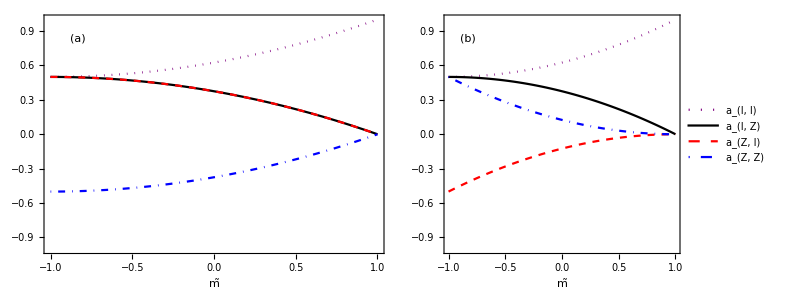

```mathematica
linestyles={{Dotted,Purple},{Automatic,Black},{Dashed,Red},{DotDashed,Blue}};(*Specify different linestyles*)
plotrangeamplitudes = {{-1,1},{-1,1}};
plotrangeamplitudesΓ = {{0,1},{-1,1}};

Grid[{{
(*Plotting as a function of m*)
Plot[DeleteCases[χerrorUpDecomposition//Flatten,0]//Evaluate,{r,-1,1},
PlotStyle->linestyles,
Frame->True,
BaseStyle->14,
PlotRange->plotrangeamplitudes,
FrameStyle->Black,
ImageSize->325,
AxesOrigin->{-1,-1},
FrameLabel->{"m̃",None},
Epilog->AlphabetLabelling["a"]],

Plot[DeleteCases[χerrorDwDecomposition//Flatten,0]//Evaluate,{r,-1,1},
PlotStyle->linestyles,Frame->True,BaseStyle->14,
PlotRange->plotrangeamplitudes,
FrameStyle->Black,
ImageSize->325,
AxesOrigin->{-1,-1},
FrameLabel->{"m̃",None},

PlotLegends->legend[{"a_(I, I)","a_(I, Z)","a_(Z, I)","a_(Z, Z)"},{0.7,0.23},LegendLayout->{"Row",2}],
Epilog->AlphabetLabelling["b"]]}}]
Export[overleafPath<>"Chap5GateErrorAmplitudes.pdf",%];
```

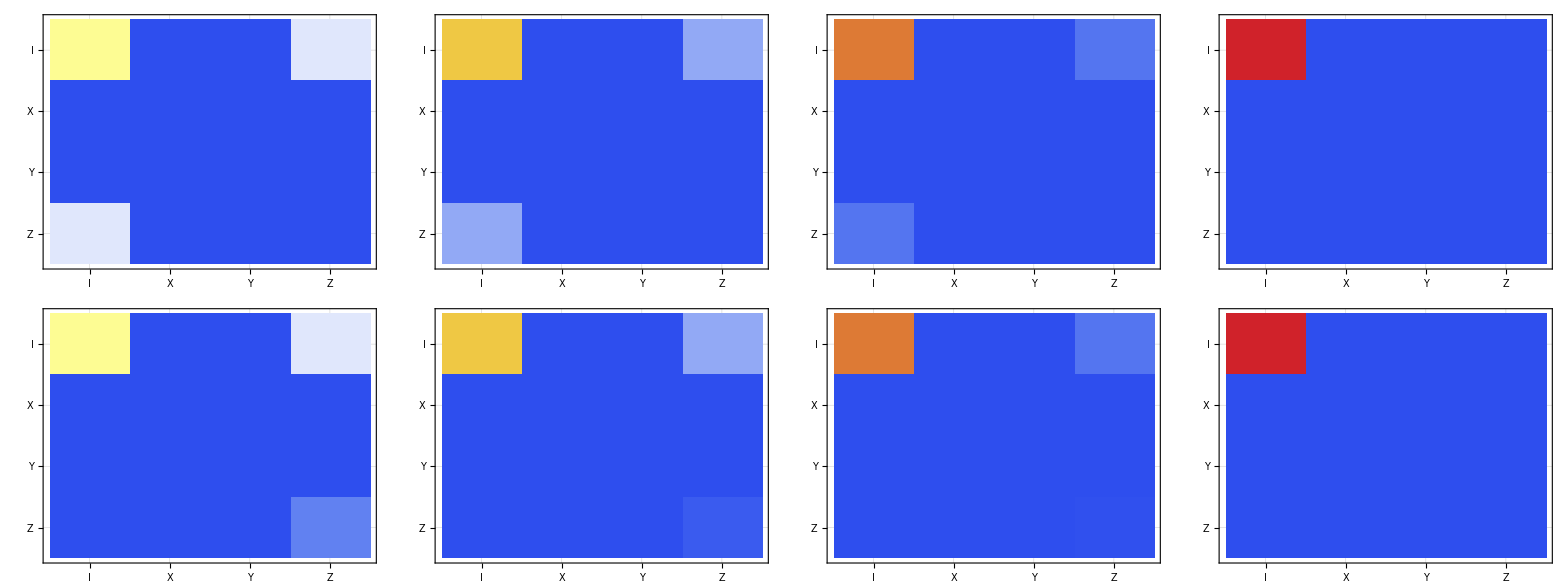

```mathematica
DecompositionXYFrameTick = {{1,"I"},{2,"X"},{3,"Y"},{4,"Z"}};
AllTicks = {DecompositionXYFrameTick,DecompositionXYFrameTick,None,None};
LowerRowTicks = {DecompositionXYFrameTick,DecompositionXYFrameTick,None,None};

Grid[{
Table[

MatrixPlot[χerrorUpDecomposition/.r->x,
ColorFunctionScaling->False,
ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1},{1,-1}]]&),
ImageSize->300,
ColorFunctionScaling->True,
FrameTicksStyle->Opacity[1],
FrameTicks->AllTicks,
(*If[x==1.,PlotLegends->Automatic,PlotLegends->None],*)
PlotTheme->"Business"],

{x,{0.,0.5,0.8,1.}}],

 Table[
MatrixPlot[χerrorDwDecomposition/.r->x,
ColorFunctionScaling->False,
ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1},{-1,1}]]&),
ImageSize->300,
ColorFunctionScaling->True,
FrameTicksStyle->Opacity[1],
FrameTicks->LowerRowTicks,
PlotTheme->"Business"
(*PlotLegends->Automatic*)],

{x,{0.,0.5,0.8,1.}}]
}]
```

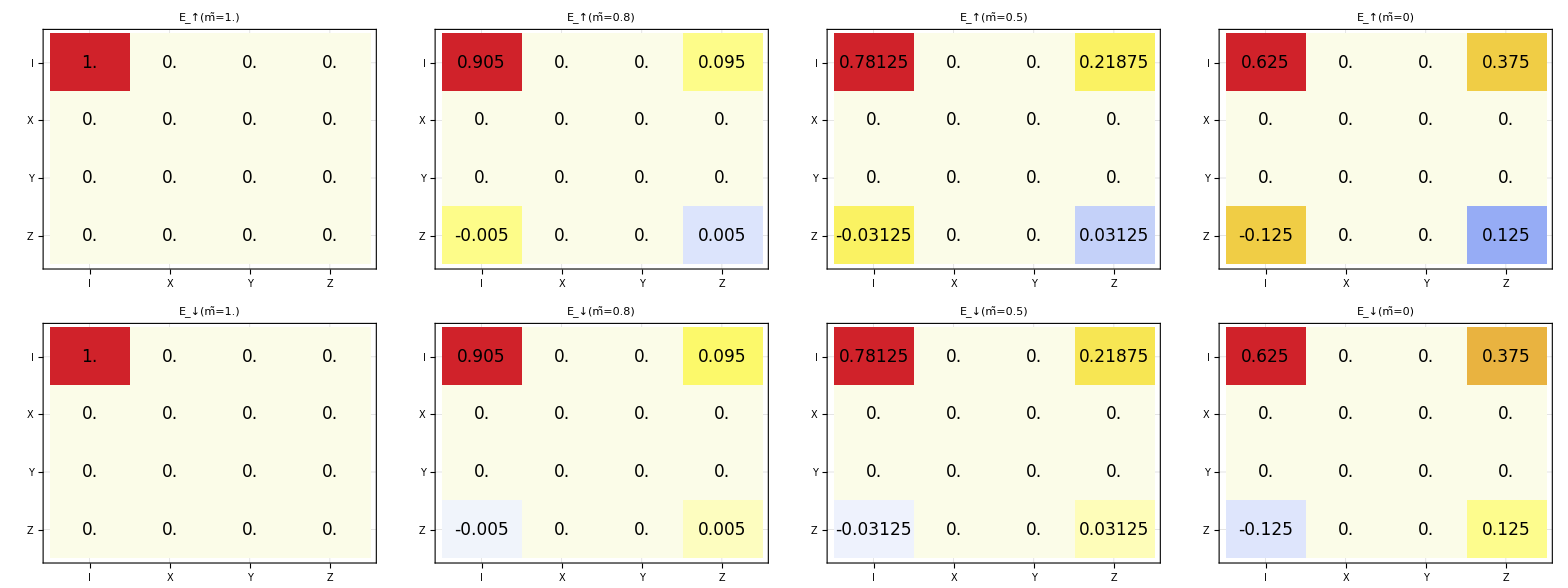

```mathematica
DecompositionXYFrameTick={{1,"I"},{2,"X"},{3,"Y"},{4,"Z"}};
AllTicks={DecompositionXYFrameTick,DecompositionXYFrameTick,None,None};
LowerRowTicks={DecompositionXYFrameTick,DecompositionXYFrameTick,None,None};

Grid[{Table[MatrixPlot[χerrorUpDecomposition/. r->x,ColorFunctionScaling->True,(*Set ColorFunctionScaling to True*)ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1},{-1,1}]]&),ImageSize->300,ColorFunctionScaling->True,FrameTicksStyle->Opacity[1],FrameTicks->AllTicks,PlotTheme->"Business",
PlotLabel->Style["E_↑(m̃="<>ToString@x<>")",Black,20,FontFamily->"Serif"],
Epilog->Table[Text[Style[χerrorDwDecomposition[[i,j]]/. r->x//N,17],{j-0.5,Length[χerrorDwDecomposition]-i+0.5}],{i,Length[χerrorDwDecomposition]},{j,Length[χerrorDwDecomposition[[i]]]}]],{x,{1.0,0.8,0.5,0}}],

Table[MatrixPlot[χerrorDwDecomposition/. r->x,ColorFunctionScaling->True,(*Set ColorFunctionScaling to True*)ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1},{-1,1}]]&),ImageSize->300,ColorFunctionScaling->True,FrameTicksStyle->Opacity[1],FrameTicks->LowerRowTicks,
PlotTheme->"Business",
PlotLabel->Style["E_↓(m̃="<>ToString@x<>")",Black,20,FontFamily->"Serif"],Epilog->Table[Text[Style[χerrorDwDecomposition[[i,j]]/. r->x//N,17],{j-0.5,Length[χerrorDwDecomposition]-i+0.5}],{i,Length[χerrorDwDecomposition]},{j,Length[χerrorDwDecomposition[[i]]]}]],{x,{1.0,0.8,0.5,0}}]}]
Export[overleafPath<>"Chap5ErrorProcessMatrixPlot.svg",%];
Export[overleafPath<>"Chap5ErrorProcessMatrixPlot.pdf",%];
```

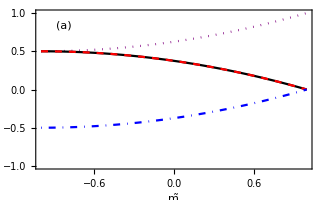
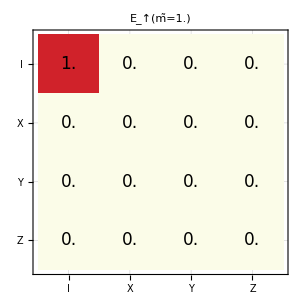
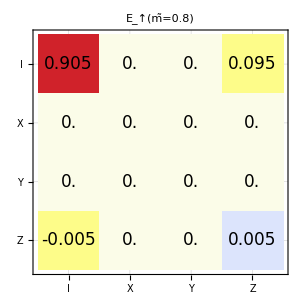
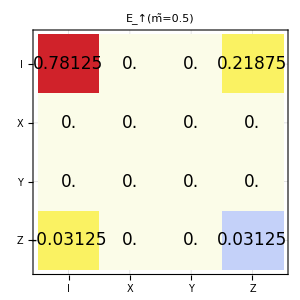
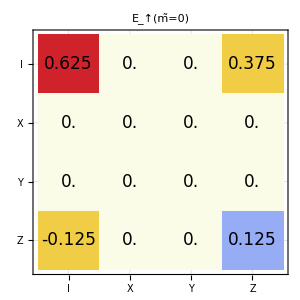
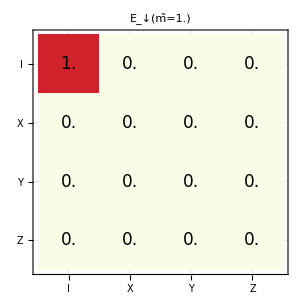
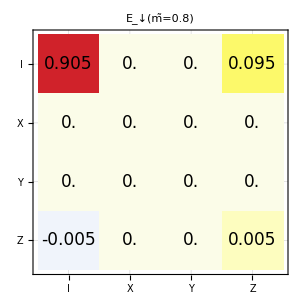
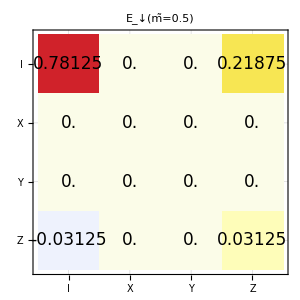
Grid[{{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{-Graphics-}]

{a}

```mathematica
Grid[{{(*Plotting as a function of m*)
Plot[DeleteCases[χerrorUpDecomposition//Flatten,0]//Evaluate,{r,-1,1},
PlotStyle->linestyles,
Frame->True,
BaseStyle->14,
PlotRange->plotrangeamplitudes,
FrameStyle->Black,
ImageSize->325,
AxesOrigin->{-1,-1},
FrameLabel->{"m̃",None},
Epilog->AlphabetLabelling["a"]],Table[MatrixPlot[χerrorUpDecomposition/. r->x,ColorFunctionScaling->True,(*Set ColorFunctionScaling to True*)ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1},{-1,1}]]&),ImageSize->300,ColorFunctionScaling->True,FrameTicksStyle->Opacity[1],FrameTicks->AllTicks,PlotTheme->"Business",
PlotLabel->Style["E_↑(m̃="<>ToString@x<>")",Black,20,FontFamily->"Serif"],
Epilog->Table[Text[Style[χerrorDwDecomposition[[i,j]]/. r->x//N,17],{j-0.5,Length[χerrorDwDecomposition]-i+0.5}],{i,Length[χerrorDwDecomposition]},{j,Length[χerrorDwDecomposition[[i]]]}]],{x,{1.0,0.8,0.5,0}}]},

Table[MatrixPlot[χerrorDwDecomposition/. r->x,ColorFunctionScaling->True,(*Set ColorFunctionScaling to True*)ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1},{-1,1}]]&),ImageSize->300,ColorFunctionScaling->True,FrameTicksStyle->Opacity[1],FrameTicks->LowerRowTicks,
PlotTheme->"Business",
PlotLabel->Style["E_↓(m̃="<>ToString@x<>")",Black,20,FontFamily->"Serif"],Epilog->Table[Text[Style[χerrorDwDecomposition[[i,j]]/. r->x//N,17],{j-0.5,Length[χerrorDwDecomposition]-i+0.5}],{i,Length[χerrorDwDecomposition]},{j,Length[χerrorDwDecomposition[[i]]]}]],{x,{1.0,0.8,0.5,0}}]},
{

Plot[DeleteCases[χerrorDwDecomposition//Flatten,0]//Evaluate,{r,-1,1},
PlotStyle->linestyles,Frame->True,BaseStyle->14,
PlotRange->plotrangeamplitudes,
FrameStyle->Black,
ImageSize->325,
AxesOrigin->{-1,-1},
FrameLabel->{"m̃",None},

PlotLegends->legend[{"a_(I, I)","a_(I, Z)","a_(Z, I)","a_(Z, Z)"},{0.7,0.23},LegendLayout->{"Row",2}],
Epilog->AlphabetLabelling["b"]]}]
```

```mathematica
erroramplitudesup= {Plot[DeleteCases[χerrorUpDecomposition//Flatten,0]//Evaluate,{r,-1,1},
PlotStyle->linestyles,
AspectRatio->5/5,
Frame->True,
BaseStyle->18,
PlotRange->plotrangeamplitudes,
FrameStyle->Black,
ImageSize->300,
AxesOrigin->{-1,-1},
FrameLabel->{"m̃",None},
Epilog->Text["↑",Scaled[{0.1,0.9}]]]};
errormatricesup=Table[MatrixPlot[χerrorUpDecomposition/. r->x,ColorFunctionScaling->True,(*Set ColorFunctionScaling to True*)ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1},{-1,1}]]&),ImageSize->300,ColorFunctionScaling->True,FrameTicksStyle->Opacity[1],FrameTicks->AllTicks,PlotTheme->"Business",
PlotLabel->Style["E_↑(m̃="<>ToString@x<>")",Black,20,FontFamily->"Serif"],
Epilog->Table[Text[Style[χerrorDwDecomposition[[i,j]]/. r->x//N,17],{j-0.5,Length[χerrorDwDecomposition]-i+0.5}],{i,Length[χerrorDwDecomposition]},{j,Length[χerrorDwDecomposition[[i]]]}]],{x,{1.0,0.8,0.5,0}}];
Do[errorplotsup=AppendTo[erroramplitudesup,errormatricesup[[j]]],{j,1,4}];
```

```mathematica
erroramplitudesdw= {Plot[DeleteCases[χerrorDwDecomposition//Flatten,0]//Evaluate,{r,-1,1},
PlotStyle->linestyles,
AspectRatio->5/5,
Frame->True,
BaseStyle->18,
PlotRange->plotrangeamplitudes,
FrameStyle->Black,
ImageSize->300,
AxesOrigin->{-1,-1},
FrameLabel->{"m̃",None},
Epilog->Text["↓",Scaled[{0.1,0.9}]]]};
errormatricesdw=Table[MatrixPlot[χerrorDwDecomposition/. r->x,ColorFunctionScaling->True,(*Set ColorFunctionScaling to True*)ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1},{-1,1}]]&),ImageSize->300,ColorFunctionScaling->True,FrameTicksStyle->Opacity[1],FrameTicks->AllTicks,PlotTheme->"Business",
PlotLabel->Style["E_↑(m̃="<>ToString@x<>")",Black,20,FontFamily->"Serif"],
Epilog->Table[Text[Style[χerrorDwDecomposition[[i,j]]/. r->x//N,17],{j-0.5,Length[χerrorDwDecomposition]-i+0.5}],{i,Length[χerrorDwDecomposition]},{j,Length[χerrorDwDecomposition[[i]]]}]],{x,{1.0,0.8,0.5,0}}];
Do[errorplotsdw=AppendTo[erroramplitudesdw,errormatricesdw[[j]]],{j,1,4}];
```

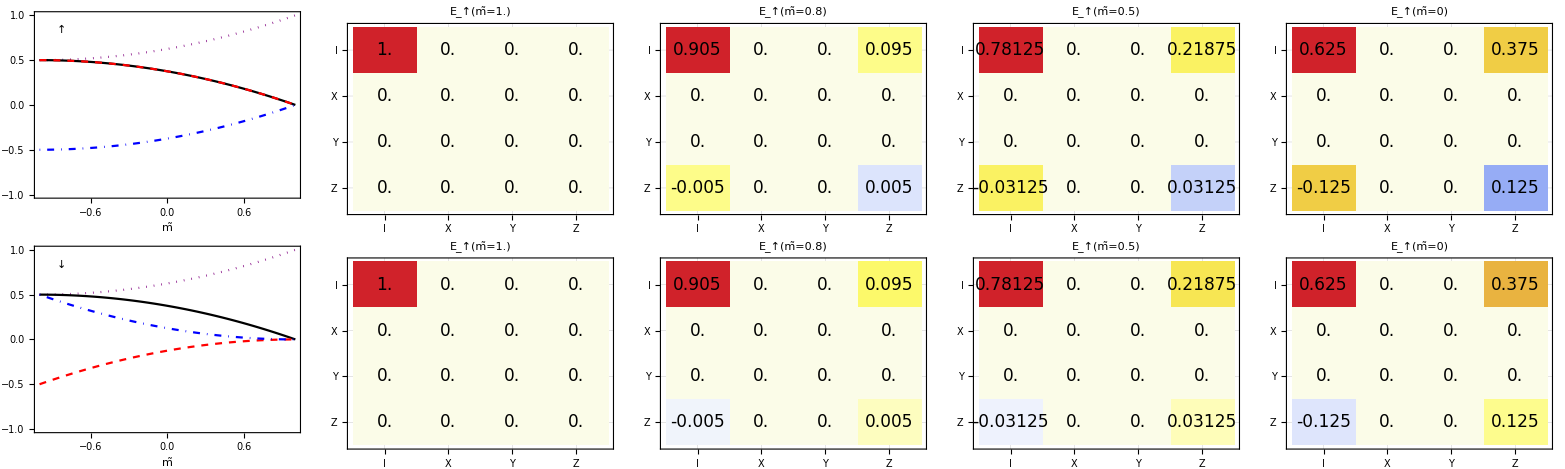

```mathematica
lastfig=Grid[{erroramplitudesup,erroramplitudesdw}]
Export[overleafPath<>"Chap5LastFigure.svg",lastfig];
Export[overleafPath<>"Chap5LastFigure.pdf",lastfig];
```